{m,Re[lower,bound,FF1],Im[lower,bound,FF1],Re[upper,bound,FF1],Im[upper,bound,FF1],Re[lower,bound,FF2],Im[lower,bound,FF2],Re[upper,bound,FF2],Im[upper,bound,FF2],Re[central,FF1],Im[central,FF1],Re[central,FF2],Im[central,FF2]}

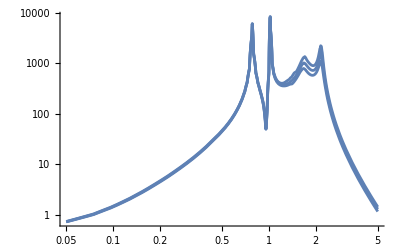

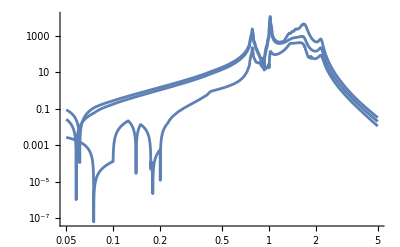

FR-form-factors-total.mx

```mathematica
SetDirectory[NotebookDirectory[]];
ffdata=Import["output.dat","Table"];
ffdata[[1]]
ffdata=Drop[ffdata,1];
F1lower[m_]=Interpolation[{#[[1]],#[[2]]+I*#[[3]]}&/@ffdata,InterpolationOrder->1][m];
F1central[m_]=Interpolation[{#[[1]],#[[10]]+I*#[[11]]}&/@ffdata,InterpolationOrder->1][m];
F1upper[m_]=Interpolation[{#[[1]],#[[4]]+I*#[[5]]}&/@ffdata,InterpolationOrder->1][m];
F2lower[m_]=Interpolation[{#[[1]],#[[6]]+I*#[[7]]}&/@ffdata,InterpolationOrder->1][m];
F2central[m_]=Interpolation[{#[[1]],#[[12]]+I*#[[13]]}&/@ffdata,InterpolationOrder->1][m];
F2upper[m_]=Interpolation[{#[[1]],#[[8]]+I*#[[9]]}&/@ffdata,InterpolationOrder->1][m];
LogLogPlot[Abs[#[m]]&/@{F1lower,F1central,F1upper},{m,0.05,5}]
LogLogPlot[Abs[#[m]]&/@{F2lower,F2central,F2upper},{m,0.05,5}]
Export["FR-form-factors-total.mx",{F1lower[mX],F1central[mX],F1upper[mX],F2lower[mX],F2central[mX],F2upper[mX]},"MX"]
```

```mathematica
ffdata[[100]]
```

{2.225,-186.308,646.672,-521.088,1052.92,-2.90274,-49.7783,284.619,99.9434,-329.639,832.415,-1.15901,-114.713}